#### The System

Here, we find any fixed points:

```mathematica
f1[x_,y_]=y^2-1 - x;
f2[x_,y_]=x^2-1 - y;
Solve[{f1[x,y]==0,f2[x,y]==0},{x,y}];
N[%]
```

{{x→-1.,y→0.},{x→0.,y→-1.},{x→-0.618034,y→-0.618034},{x→1.61803,y→1.61803}}

And plot the vector field, from which it looks like the (0,-1) is a stable point:

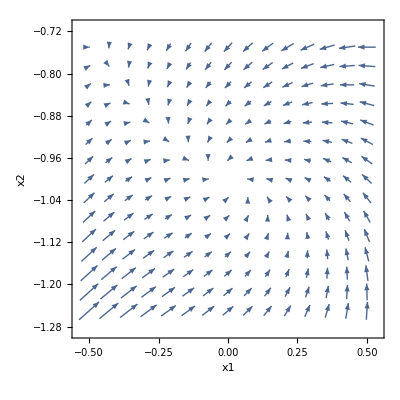

```mathematica
field=VectorPlot[{f1[x,y],f2[x,y]},{x,-0.5,0.5},{y,-1.25,-0.75},Frame->True,FrameLabel->{"x1","x2"},AspectRatio->1]
```

{{0,0.5,-1.},{1,0.,-0.75},{2,-0.4375,-1.},{3,0.,-0.808594},{4,-0.346176,-1.},{5,0.,-0.880162},{6,-0.225315,-1.},{7,0.,-0.949233},{8,-0.0989562,-1.},{9,0.,-0.990208},{10,-0.0194888,-1.}}

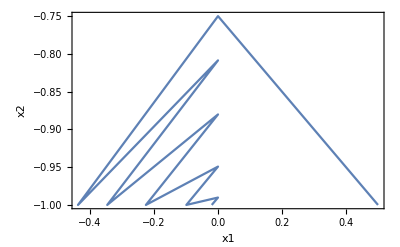

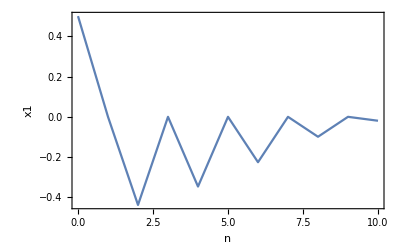

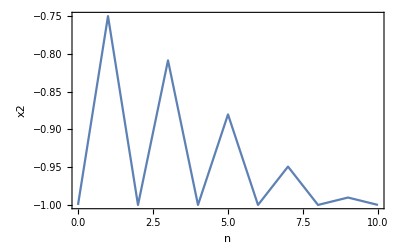

```mathematica
Clear[x1,x2]
x1[0]:= α1
x2[0]:= α2
x1[n_]:= x1[n] = f1[x1[n-1],x2[n-1]]+x1[n-1]
x2[n_]:= x2[n] = f2[x1[n-1],x2[n-1]]+x2[n-1]
num = 10;
data = Table[{n,x1[n],x2[n]},{n,0,num}];
data = data /. α1->0.5 /.α2->-1.0
phase = Table[{Part[data,n+1,2],Part[data,n+1,3]},{n,0,num}];
datax1 = Table[{Part[data,n+1,1],Part[data,n+1,2]},{n,0,num}];
datax2 = Table[{Part[data,n+1,1],Part[data,n+1,3]},{n,0,num}];
ListPlot[phase,Joined->True,Frame->True,FrameLabel->{"x1","x2"}]
ListPlot[datax1,Joined->True,Frame->True,FrameLabel->{"n","x1"}]
ListPlot[datax2,Joined->True,Frame->True,FrameLabel->{"n","x2"}]
```